# Bayesian Statistics and Econometrics using Mathematica

## A work in progress

Mark Fisher
Research

Federal Reserve Bank of Atlanta

The views expressed are those of the author and do not necessarily represent those of the Federal Reserve Bank of Atlanta or the Federal Reserve System.

|     ▶

## Outline

### This talk will illustrate how I use Mathematica for Bayesian statistical and econometric analysis

#### Bayesian statistical techniques are numerically intensive

Extensive use of Compile

Problems with running out of RAM

Parallelization and GridMathematica

#### Review and illustrate some Markov Chain Monte Carlo (MCMC) techniques

Random-walk Metropolis algorithm

Gibbs sampling

Reversible Jump MCMC (for model averaging)

Particle filters (for dynamic models with latent state variables)

Using "bridge estimator" to compute the likelihood of a model from MCMC output

#### Applications

Inferring probabilities of the target fed funds rate from options on fed funds futures contracts (illustrates Reversible Jump MCMC and particle filters)

Unit root tests of Purchasing Power Parity (illustrates Bayesian hypothesis testing and maximum entropy priors)

Batting averages and hitting streaks in baseball (illustrates hierarchical models and Markov-switching models)

#### Alternative software

More or less dedicated: WinBUGS, R (umacs and rv), BACC (WinR), JAGS (Just Another Gibbs Sampler)

Non-dedicated competitors: Matlab (main one for economists), C, and FORTRAN

Possible connectivity via J/Link and .NET/Link

#### Wish list

Bayesian statistical techniques use probability distributions that are not included. Need more built in. Dirichlet distribution. t-distribution with scale and location parameters.

Need to compile NormalDistribution, GammaDistribution, etc.

Have MCMC tools built into Mathematica

◀     |     ▶

## Fathers of Bayesian Analysis

```mathematica
Row[{Labeled[Show[BayesImage,Frame->True,FrameTicks->False,ImageSize->{300,300}],Style["Thomas Bayes","Subtitle"],Top],Labeled[Show[LaplaceImage,Frame->True,FrameTicks->False,ImageSize->{300,300}],Style["Pierre-Simon Laplace","Subtitle"],Top]}]
```

Thomas Bayes
-Graphics-Pierre-Simon Laplace
-Graphics-

◀     |     ▶

## Costs and Benefits of Bayesian Analysis (versus classical/frequentist approach to inference)

### Benefits

#### Can make probability statements about parameters and models

#### Great flexibility

#### Small-sample distributions

### Costs

#### Need a prior distribuion for unobservables (such as parameters, missing data, competing models)

#### Computationally intensive

### Bottom line

#### You get what you pay for

#### There's no free lunch

◀     |     ▶

### Also note

#### The cost of doing Bayesian analysis is going down and down (with the cost of computation)

#### According to the law of demand, more and more Bayesian analysis will be "consumed"

If you're not a Bayesian, your kids will be

## Examples (projects I'm working on)

### Euro area Purchasing Power Parity (PPP), monthly data since mid-1950s

#### Is the AR coefficient (1) less than 1 or (2) equal to 1 [mean-reverting vs. random walk]

y_t==α+β y_(t-1)+ϵ_t,    ϵ_t∼N[0,σ]

Frequentist/classical: Nonstandard distribution if β=1

For Bayesian, easy to impose β∈[0,1], use truncated Gaussian prior for β

150-years of annual data indicate mean-reverting, while 50 years of month data indicate random-walk (using frequentist approach)

### Inferring probabilities of fed funds target rate from options on futures contract

Y=Xβ+ϵ,       ϵ∼N[0,σI]

Y is n×1 vector of option prices

X is n×k matrix of option payouts

β is k×1 vector of probabilities, so that 0≤β_j≤1 and ∑β_j=1 (β lies on simplex)

β_j is the probability that the target fed funds rate (set by the Federal Reserve) equals r^*=s_j (for example, r^*=4.75 percent)

### Batting averages and hitting streaks in baseball

Albright (1993) JASA, 501-player seasons from 1987-1990 (both leagues). "Regular" players (each with > 500 at-bats/season)

Are there hitting streaks?

#### Frequentist approach

"Runs test": Count the number of runs of consecutive successes and failures. Streaks means fewer runs.

Conclusion: Can't reject the null hypothesis of "no streaks", which is taken to mean no streaks

```mathematica
data=RandomInteger[BernoulliDistribution[.275],600]
```

{0,1,0,0,0,0,0,0,0,1,0,1,0,1,1,0,0,0,1,0,0,0,0,1,1,0,1,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,1,1,1,0,1,0,0,0,1,0,0,0,0,0,0,0,0,1,1,1,0,0,1,1,0,1,1,0,0,0,0,1,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,1,0,0,1,0,1,1,0,0,0,0,1,0,0,0,1,0,0,0,0,1,0,0,1,1,0,1,0,1,0,0,0,1,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,0,0,0,0,0,0,0,1,0,1,0,1,1,0,0,0,0,0,0,0,1,1,1,0,1,0,0,1,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,1,0,0,1,0,0,0,1,0,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0,1,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0,0,0,0,1,1,1,1,0,0,1,0,0,0,0,0,1,0,1,1,1,1,0,0,0,0,0,1,0,1,1,1,1,0,0,0,1,0,1,0,1,0,0,0,1,0,1,0,1,0,1,0,0,0,1,0,1,0,1,0,1,0,0,0,1,0,0,0,1,0,0,0,0,0,1,0,0,0,0,1,1,0,1,0,0,0,1,0,0,0,0,0,1,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,1,0,0,1,1,0,1,0,1,0,0,0,0,1,1,0,0,1,0,0,0,1,0,1,0,0,1,0,1,0,1,1,0,0,0,0,1,0,0,0,1,0,0,0,0,0,0,1,0,1,1,0,1,0,0,1,1,0,0,0,1,0,0,0,0,0,0,0,0,1,1,1,1,0,0,0,0,1,0,0,0,0,1,0,0,0,1,0,1,1,1,0,0,0,1,1,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,1,0,1,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,1,1,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,0,1,0,0,0,0,0,0,1,0,0,0,0,0,0,1,0,0,0,1,0,0,0,0,0,0,0,1,0,0,1,0,1,0,0,0,0,1,0,0,0,0,1,1,0,0,0,0,0,0,0,0,1,0,0,0,0,1,0,0,1,0,1,1,0,1,1,0,1,1,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0,0,1}

```mathematica
Length[Split[data]]
```

246

```mathematica
sim=Table[Length[Split[RandomInteger[BernoulliDistribution[.275],600]]],{10^4}];
```

```mathematica
<<Version6`SmoothedHistogram`
```

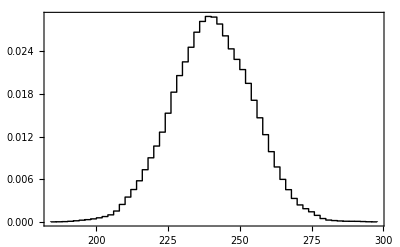

```mathematica
SmoothedHistogram[sim,2,3]
```

Note, did this assuming we knew the true batting average (we conditioned on an unobservable)

#### Bayesian approach

It takes a model to beat a model

Markov switch models: two states: hot and cold with conditional probabilities of switching and staying:

Two unobserved states: hot and cold

Conditional probabilities of switching and staying:

```mathematica
({{1-p, p}, {q, 1-q}})
```

Compare probability of no-streak model with probability of Markov-switching model

Eqaul probabilities means it's just as likely there are streaks as not

The problem is complicated by "situational variables" such as home/away, day/night, grass/artificial, and most importantly the pitcher (ERA, left or right handed)

◀     |     ▶

## Bayesian updating

Bayesian approach

Unknowns: Model parameters, latent state variable, missing observations, etc.

Use probability distributions to represent information about unknowns.

Use probability theory to characterize uncertainty and to update given new information (i.e., new data).

Let θ denote unknown parameters and let Y denote new data.

Let p(θ) denote prior probability distribution (continuous and/or discrete)

Let p(θ|Y) denote posterior probability distribution

Let p(Y) denote (marginal) likelihood of the data (according to the given model)

### Bayesian updating

p(θ) ⟶ p(θ|Y)

### Bayes' theorem/rule

p (θ|Y)=(p (Y|θ) p(θ))/(p (Y))∝p(Y|θ)p(θ)

where

p(y)==∫p(Y|θ) p(θ)ⅆθ

### Bayes factor for comparing two models

#### The ratio of the likelihood of the data for the two models

(p_1(y))/(p_2(y))

◀     |     ▶

## Bayesian updating illustration

```mathematica
<<Version6`SmoothedHistogram`
```

```mathematica
Needs["ErrorBarPlots`"]
```

```mathematica
data=RandomReal[NormalDistribution[1,1],30]
```

{1.47665,0.603016,1.20322,1.94178,0.011728,1.28277,1.52457,1.82858,0.583614,0.855543,1.55552,0.528226,-0.327389,2.21422,1.30468,0.722108,1.54371,-0.23283,0.401888,1.50529,1.32672,0.961569,1.31155,0.225611,0.951423,1.22246,-1.35765,1.15293,1.29899,2.67915}

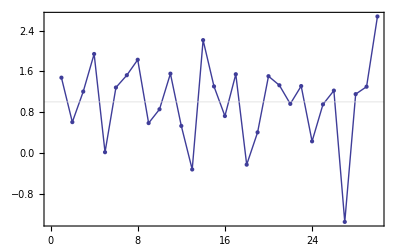

```mathematica
ListLinePlot[data,Mesh->All,GridLines->{{},{1}}]
```

Model

y_j=μ+ϵ_j,   ϵ_j∼N(0,1)

```mathematica
PDF[NormalDistribution[0,1],Subscript[y, j]-μ]
```

(ⅇ^(-1/2 (-μ+y_j)^2))/(√(2 π))

#### Analytical approach

```mathematica
pdfs=PDF[NormalDistribution[0,1],data-μ]
```

{(ⅇ^(-1/2 (1.47665-μ)^2))/(√(2 π)),(ⅇ^(-1/2 (0.603016-μ)^2))/(√(2 π)),(ⅇ^(-1/2 (1.20322-μ)^2))/(√(2 π)),(ⅇ^(-1/2 (1.94178-μ)^2))/(√(2 π)),(ⅇ^(-1/2 (0.011728-μ)^2))/(√(2 π)),(ⅇ^(-1/2 (1.28277-μ)^2))/(√(2 π)),(ⅇ^(-1/2 (1.52457-μ)^2))/(√(2 π)),(ⅇ^(-1/2 (1.82858-μ)^2))/(√(2 π)),(ⅇ^(-1/2 (0.583614-μ)^2))/(√(2 π)),(ⅇ^(-1/2 (0.855543-μ)^2))/(√(2 π)),(ⅇ^(-1/2 (1.55552-μ)^2))/(√(2 π)),(ⅇ^(-1/2 (0.528226-μ)^2))/(√(2 π)),(ⅇ^(-1/2 (-0.327389-μ)^2))/(√(2 π)),(ⅇ^(-1/2 (2.21422-μ)^2))/(√(2 π)),(ⅇ^(-1/2 (1.30468-μ)^2))/(√(2 π)),(ⅇ^(-1/2 (0.722108-μ)^2))/(√(2 π)),(ⅇ^(-1/2 (1.54371-μ)^2))/(√(2 π)),(ⅇ^(-1/2 (-0.23283-μ)^2))/(√(2 π)),(ⅇ^(-1/2 (0.401888-μ)^2))/(√(2 π)),(ⅇ^(-1/2 (1.50529-μ)^2))/(√(2 π)),(ⅇ^(-1/2 (1.32672-μ)^2))/(√(2 π)),(ⅇ^(-1/2 (0.961569-μ)^2))/(√(2 π)),(ⅇ^(-1/2 (1.31155-μ)^2))/(√(2 π)),(ⅇ^(-1/2 (0.225611-μ)^2))/(√(2 π)),(ⅇ^(-1/2 (0.951423-μ)^2))/(√(2 π)),(ⅇ^(-1/2 (1.22246-μ)^2))/(√(2 π)),(ⅇ^(-1/2 (-1.35765-μ)^2))/(√(2 π)),(ⅇ^(-1/2 (1.15293-μ)^2))/(√(2 π)),(ⅇ^(-1/2 (1.29899-μ)^2))/(√(2 π)),(ⅇ^(-1/2 (2.67915-μ)^2))/(√(2 π))}

```mathematica
fun=Function[μ,Times@@pdfs//Simplify//Evaluate]
```

Function[μ,1.60311×10^-23 ⅇ^(30.2997 μ-15. μ^2)]

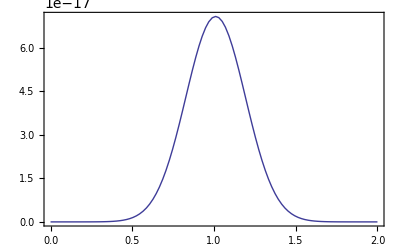

```mathematica
Plot[fun[μ],{μ,0,2},PlotPoints->100,PlotStyle->Thick]
```

Prior for μ:

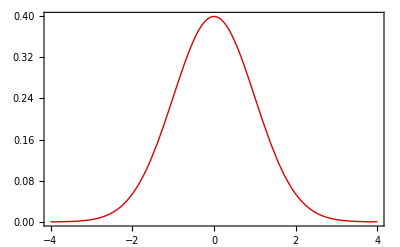

```mathematica
plot0=Plot[PDF[NormalDistribution[0,1],μ],{μ,-4,4},PlotStyle->Directive[Thick,ColorData[2][1]]]
```

```mathematica
int=NIntegrate[fun[μ]PDF[NormalDistribution[0,1],μ],{μ,0,2}]
```

7.76483×10^-18

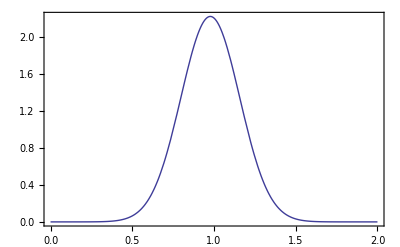

```mathematica
plot1=Plot[fun[μ]PDF[NormalDistribution[0,1],μ]/int,{μ,0,2},PlotStyle->Thick]
```

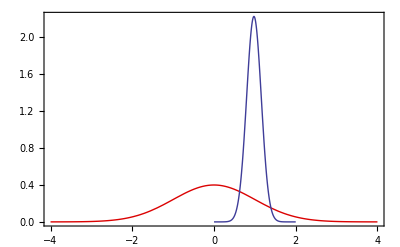

```mathematica
Show[plot0,plot1,PlotRange->All]
```

#### Numerical approach

(This doesn't work with improper prior.)

```mathematica
swarm0=RandomReal[NormalDistribution[0,1],10^5];
```

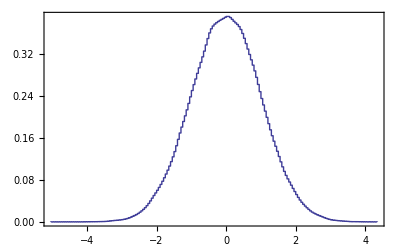

```mathematica
histo0=SmoothedHistogram[swarm0,.05,5,PlotStyle->Directive[Thick,ColorData[1][1]]]
```

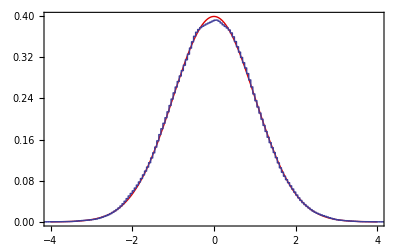

```mathematica
Show[plot0,histo0]
```

Bayesian updating:

```mathematica
swarm1=RandomChoice[(fun/@swarm0)->swarm0,Length[swarm0]];
```

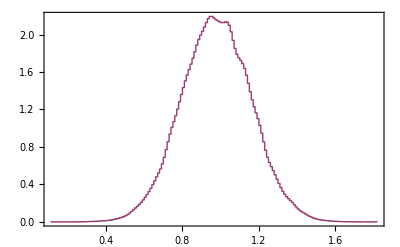

```mathematica
histo1=SmoothedHistogram[swarm1,.01,5,PlotStyle->Directive[Thick,ColorData[1][2]]]
```

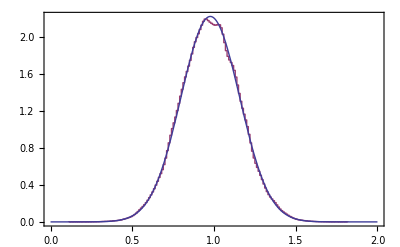

```mathematica
Show[histo1,plot1]
```

```mathematica
pdffuns=Function/@(pdfs/.μ->#);
updated=FoldList[RandomChoice[Map[#2,#1]->#1,Length[#1]]&,swarm0,pdffuns];
meansd=Through[{Mean,StandardDeviation}[#]]&/@updated;
```

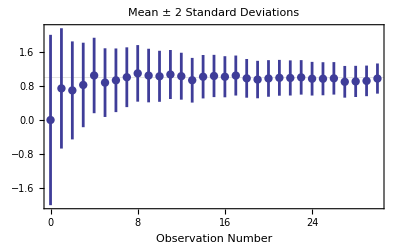

```mathematica
errorbars=Cases[Transpose[{Range[0,30],meansd}],{i_,{m_,s_}}:>{{i,m},ErrorBar[2s]}];
ErrorListPlot[errorbars,GridLines->{{},{1}},PlotLabel->"Mean ± 2 Standard Deviations",FrameLabel->{"Observation Number",None},PlotStyle->Directive[PointSize[.015],Thickness[.005]]]
```

```mathematica
ListAnimate[SmoothedHistogram[#,.05,5,PlotRange->{{-3.25,3.25},{0,2.3}},PlotRangePadding->Scaled[0],PlotRangeClipping->True,GridLines->{{1},{}}]&/@updated]
```

#### Particle filter

Suppose μ wasn't constant, but was a moving target

```mathematica
Subscript[μ, t]==α+β Subscript[μ, t-1]+Subscript[u, t]
```

Then use the law of motion to update each particle before the next update with the "measurement equation"

If shocks are Gaussian and equations are linear (as in this example), then the Kalman filter is Bayesian updating

But the particle filter works in all cases, non-Gaussian and nonlinear

(Sequential MCMC techniques)

◀     |     ▶

## Metropolis illustration

### Markov Chain Monte Carlo (MCMC)

I borrowed this example from the Demonstrations web site

```mathematica
Contributed by:Philip Gregory (Physics and Astronomy,University of British Columbia)
```

```mathematica
<<Version6`RandomWalkMetropolis`
<<Version6`BinnedKernelDensity`
```

```mathematica
kernel=0.087 ⅇ^(1/2 (-(x-4) (0.595(x-4)-0.238 (y-3))-(-0.238(x-4)+0.595 (y-3))  (y-3)))+(ⅇ^(1/2 (-x^2-y^2)))/(2 π);
```

```mathematica
xyint=NIntegrate[kernel,{x,-∞,∞},{y,-∞,∞}]
```

2.0024

```mathematica
Plot3D[kernel,{x,-5,10},{y,-5,10},PlotRange->Full,PlotPoints->45,SphericalRegion->True,Axes->{True,True,False}]
```

-Graphics3D-

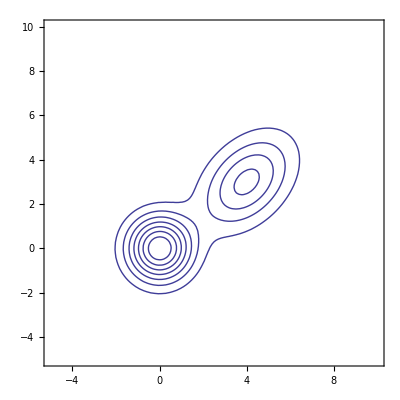

```mathematica
pdfcontours=ContourPlot[kernel,{x,-5,10},{y,-5,10},PlotRange->Full,ContourShading->False,PlotPoints->45,ContourStyle->Directive[Thick,ColorData[1][1]]]
```

```mathematica
expr=Log[kernel/.{x->z[[1]],y->z[[2]]}]//Quiet;
```

```mathematica
With[{
sigma=.2,
ndraws=1000,
burnin=0,
thin=1
},
mc=RandomWalkMetropolis[
expr, (* log of pdf *)
{z, (* z represents vector of parameters *)
{-4,9}}, (* starting values *)
sigma, (* average size of proposal step *)
ndraws, (* number of draws *)
BurnInNumber->burnin, (* number to drop from beginning *)
ThinningNumber->thin, (* keep 1 per this number of draws *)
InBoundsQ->(True&) (* the region over which expr is well-defined *)
]]; 
AcceptanceRate[mc]
```

0.862

```mathematica
Dimensions[mc]
```

{1000,2}

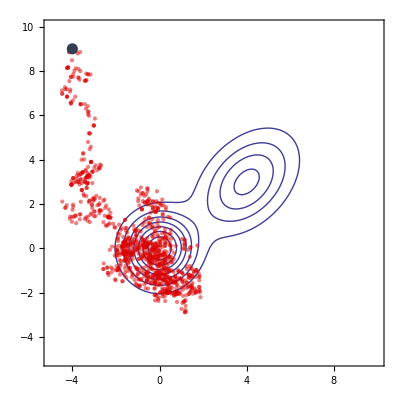

```mathematica
Show[pdfcontours,Epilog->{ColorData[2][1],Opacity[.5],Point[mc],Opacity[1],PointSize[.02],ColorData[2][7],Point[{-4,9}]}]
```

Diagnostics:

```mathematica
feverrow={ListLinePlot[mc[[All,1]],PlotLabel->Style["x",Italic]],ListLinePlot[mc[[All,2]],PlotLabel->Style["y",Italic]]};
historow={SmoothedHistogram[mc[[All,1]],.3,3,PlotLabel->Style["x",Italic]],SmoothedHistogram[mc[[All,2]],.3,3,PlotLabel->Style["y",Italic]]};
```

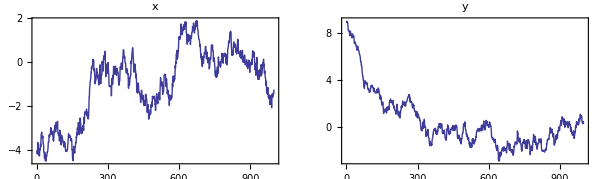
Visualize Serial Correlation
-Graphics-

```mathematica
Labeled[GraphicsRow[feverrow,ImageSize->600],Style["Visualize Serial Correlation",18,FontFamily->"Times"],Top]
```

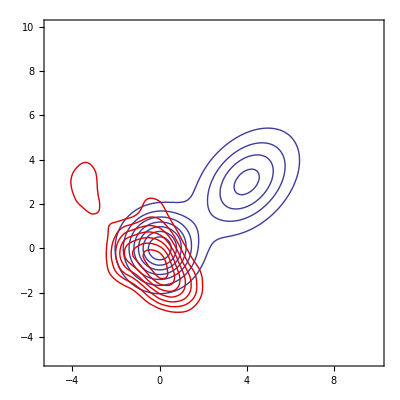

```mathematica
Show[pdfcontours,BinnedKernelDensityPlot[mc,BinwidthFactor->3,ImageSize->400,PlotType->ContourPlot,PlotRange->{.01,All},ContourShading->False,ContourStyle->ColorData[2][1]]]
```

```mathematica
BinnedKernelDensityPlot[mc,BinwidthFactor->3,Axes->{True,True,False},SphericalRegion->True,ImageSize->400]
```

-Graphics3D-

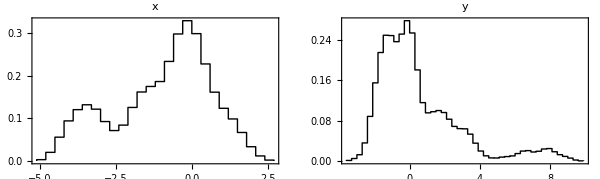
Marginal Distributions
-Graphics-

```mathematica
Labeled[GraphicsRow[historow,ImageSize->600],Style["Marginal Distributions",18,FontFamily->"Times"],Top]
```

```mathematica
SeparatedPartialMeans[#,4,20]&/@Transpose[mc]
```

{5.01821×10^-14,0.}

◀     |     ▶

## RandomWalkMetropolis code snippets

```mathematica
CompileMCMCFunction[nfun_,start_,nDraws_,nThin_,nBurn_,patt_] :=
	Compile[{}, (* no args *)
	Rest@NestList[
		Nest[nfun,#,nThin]&, (* thinning *)
		Nest[nfun,start,nBurn], (* burn-in *)
		nDraws],
	patt] (* for stuff that doesn't compile, maybe *)
```

```mathematica
AssembleNestFunction[vfun_,bfun_,step_] := (* assemble the function to nest *)
	Function[s, (* parameter values (Most) and function value (Last) *)
	Module[{p,pval},
		p = Most[s] + step[]; (* generate proposal with random-walk step *)
		If[bfun[p], 
			(* the proposal is in bounds *)
			pval = vfun[p]; (* value function *)
			If[pval - Last[s] ≥ Log[RandomReal[]],
				Append[p,pval], (* accept proposal *)
				s], (* reject proposal *)
			(* the proposal is out of bounds *)
			s] 
	]]
```

```mathematica
AssembleStepFunction[chol_,k_,df_] := (* assemble sfun *)
	Switch[df, (* degrees of freedom *)
		Infinity, (* normal proposal *)
		Function[{}, 
			Table[Sqrt[-2 Log[RandomReal[]]] Cos[2 Pi RandomReal[]],{k}].chol (* cholesky *)
			],
		_, (* t proposal *)
		Function[{},
			(1/Sqrt[(#.#)&[Table[Sqrt[-2 Log[RandomReal[]]] Cos[2 Pi RandomReal[]],{df}]]/df]*
				Table[Sqrt[-2 Log[RandomReal[]]] Cos[2 Pi RandomReal[]],{k}]).chol
			]
		]
```

◀     |     ▶

## Inferring the probabilities for the target fed funds rate from options on fed funds futures

Fed funds rate is rate banks charge each other for unsecured overnight loans

Federal Open Market Committee (FOMC) conducts monetary policy by setting a target fed

Open Market Desk at Federal Reserve Bank of New York (FRBNY) undertakes operations to keep the daily effective funds rate close to the target

There are futures contracts traded on month-average daily effective fed funds rate

There are put and call options traded on the futures contracts

Asset pricing theory expresses the value of an option as the expected payout (discounted at the risk-free rate) computed using "risk-neutral" probabilities

v_i=θ E^Q[X_i]

v_i is the value of the i^th option, θ is discount factor, E^Q[ ] is expectations operator using risk-neutral probabilities, and X_i is the vector of payouts

X_ij is the payout to the i^th option in the j^th "state" (e.g., if the target rate turns out to 4.50 percent)

y=Xβ+ϵ

ϵ is "measurement" error, where ϵ∼N(0,σI)

Marginal likelihood for β

```mathematica
Transpose[(y-X.β)] .(y-X.β)^(-n/2)
```

Example of MCMC output

◀     |     ▶

## Reversible Jump Illustration

### Draw from two distributions separately (uniform in 1 dimension and uniform in 2 dimensions)

```mathematica
<<Version6`RandomWalkMetropolis`
<<Version6`SmoothedHistogram`
```

```mathematica
mc1=RandomWalkMetropolis[
Log[1], (* an arbitrary constant *)
{z,{.5}},.1,10^5,
InBoundsQ->(0≤#1[[1]]≤1&)];
AcceptanceRate[mc1]
```

0.91988

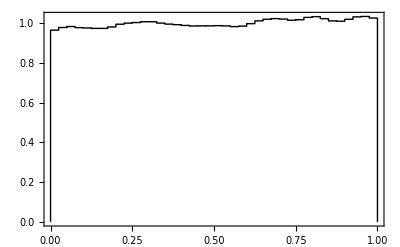

```mathematica
SmoothedHistogram[mc1[[All,1]],{0,1,.025},3,Overhang->None]
```

```mathematica
mc2=RandomWalkMetropolis[
Log[2], (* a constant *)
{z,{.5,.25}},.1,10^5,
InBoundsQ->(0≤#[[1]]≤1&&0≤#[[2]]≤#[[1]]&)
];
AcceptanceRate[mc2]
```

0.75343

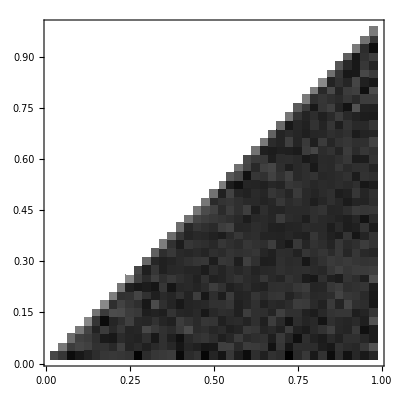

```mathematica
SmoothedHistogram[mc2,.025]
```

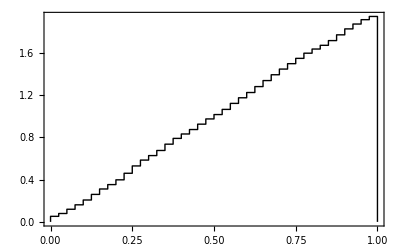

```mathematica
SmoothedHistogram[mc2[[All,1]],{0,1,.025},3,Overhang->None]
```

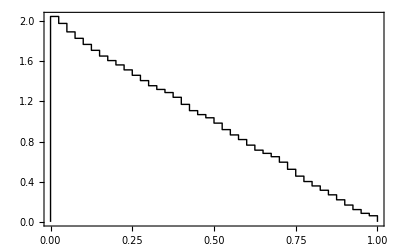

```mathematica
SmoothedHistogram[mc2[[All,2]],{0,1,.025},3,Overhang->None]
```

### Reversible jump MCMC

State s = (model,x,y), where model is either 1 or 2 and (x,y) are coordinates (if model=1, then y=0).

r is the across-model jump-probability adjustment factor (depends on density of proposal and Jacobian of transformation)

```mathematica
mcmcfun=Function[{s,r},
Module[{model,x,y,switch,xp,yp},
{model,x,y}=s;
switch=RandomInteger[];
If[model==1,
If[switch==0, (* try switching to model 2 *)
yp=RandomReal[x]; (* uniform draw from [0, x] *)
If[Random[]<r, (* jump probability adjustment factor *)
{2,x,yp}, (* accept point in model 2 *)
s], (* keep point in model 1 *)
(* else draw from model 1 *)
xp=RandomReal[NormalDistribution[x,.1]]; (* random-walk proposal *)
If[0≤xp≤1,
{model,xp,0}, (* accept new point in model 1 *)
s]], (* reject new point in model 1 *)
(* else model == 2 *)
If[switch==0, (* try switching to model 1 *)
If[Random[]<1/r,(* jump probability adjustment factor for reverse jump *)
{1,x,0},
s],
(* else draw from model 2 *)
xp=RandomReal[NormalDistribution[x,.1]];
yp=RandomReal[NormalDistribution[y,.1]];
If[0≤xp≤1&&0≤yp≤xp,
{model,xp,yp},
s]]
]
]];
```

Set adjustment factor to r = 2 x in order to get equal numbers of draws from each model

```mathematica
sim=Rest@NestList[
mcmcfun[#,2#[[2]]]&, (* adjustment factor: r = 2 x*)
{1,RandomReal[],0},
10^5];
```

```mathematica
Count[sim,{2,__}]
```

50674

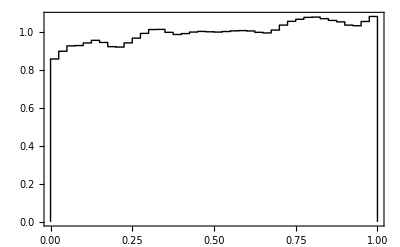

```mathematica
SmoothedHistogram[Cases[sim,{1,x_,_}:>x],{0,1,.025},3,Overhang->None]
```

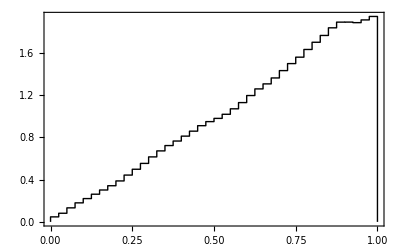

```mathematica
SmoothedHistogram[Cases[sim,{2,x_,_}:>x],{0,1,.025},3,Overhang->None]
```

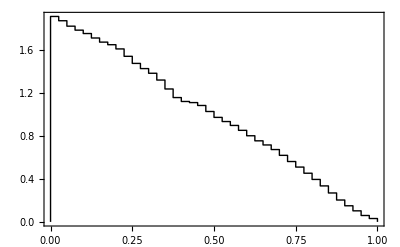

```mathematica
SmoothedHistogram[Cases[sim,{2,_,y_}:>y],{0,1,.025},3,Overhang->None]
```

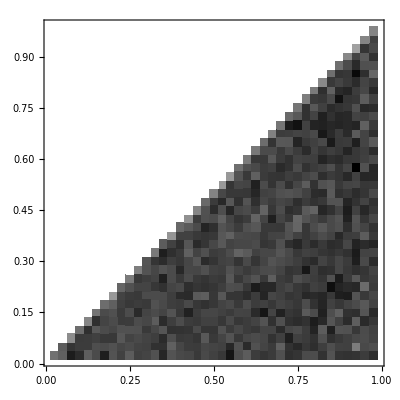

```mathematica
SmoothedHistogram[Cases[sim,{2,x_,y_}:>{x,y}],.025]
```

```mathematica
ListAnimate[Table[Graphics[GraphicsComplex[sim[[5000;;5000+n]][[All,{2,3}]],{Line[Range[n]],Point[Range[n]],Red,PointSize[.02],Point[n]}],AspectRatio->Automatic,PlotRange->{{0,1},{0,1}},Frame->True,PlotRangePadding->Scaled[.025]],
{n,200}
]]
```

```mathematica
With[{pts=sim[[500;;-1;;500]][[All,{2,3}]]},ListAnimate[Table[Graphics[GraphicsComplex[pts,{Opacity[.5],Point[Range[n]]}],AspectRatio->Automatic,PlotRange->{{0,1},{0,1}},Frame->True,PlotRangePadding->Scaled[.025]],
{n,200}
]]]
```

◀     |     ▶

## The End

◀     |     ▶